```mathematica
SetDirectory["/home/dschiebe/Documents/lanayru/PhD_Files/HexaBox_102PureIntsDone"];
PureIntegralsOld=ReadList[FileNameJoin[{Directory[],"files/PureIntegralBasis1-111.txt"}]];
PureIntegralsNew=ReadList[FileNameJoin[{Directory[],"files/PureIntegralBasis1-119.txt"}]];
Get[FileNameJoin[{Directory[],"HexaBoxModules.m"}]];
$P=2^31-1;
$P=2^31-1;
CayleyEntry[i_,j_]:=Module[{mat},
If[i==0 && j==0 ,
Return[0];
];
If[i==0 || j==0 ,
Return[1];
];

If[i==j,
mat=2msq[i]/.intMasses;
Return[mat];
];
If[i<j,
mat=((msq[i]/.intMasses)+(msq[j]/.intMasses)-Expand[(Sum[q[n],{n,i,j-1}])^2])/.mandelstamScalarProducts/.kinematics;
Return[mat];
];
If[i>j,
mat=CayleyEntry[j,i];
Return[mat];
];
]
cutCayley[mat_,l_]:=Module[{res},
res=mat;
res=Delete[res,l];
res=Transpose[Delete[Transpose[res],l]];
res
]
```

{hxb[-1,1,0,1,0,1,0,1,0,0,0,0,0],hxb[0,1,0,1,0,1,0,1,0,0,0,0,0],hxb[1,0,0,1,0,1,0,1,-1,0,0,0,0],hxb[1,0,0,1,0,1,0,1,0,0,0,0,0]}

{123,141,158,159}

# Diagram 158/159 (Basis1-119)

hxb[1,0,0,1,0,1,0,1,-1,0,0,0,0]

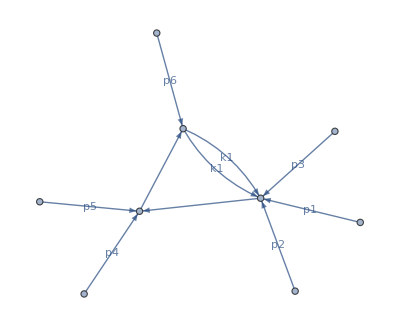

```mathematica
PureIntegralsNew[[158]]
plotDiagram[PureIntegralsNew[[158]]]
```

```mathematica
q[1]=p[5]+p[4]/.p4cons;
q[2]=p[1]+p[2]+p[3];
q[3]=-q[1]-q[2];
intMasses={msq[1]->mt2,msq[2]->0,msq[3]->0};
modcayleyMat=Table[CayleyEntry[i,j],{i,0,3},{j,0,3}];
modcayleyMat//MatrixForm
kP=3+1;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]
convchange={v23->Expand[2 p[5]p[4]]/.mandelstamScalarProducts/.kinematics,q2->0,v45->s123};
BasisChange[1]=ep^3/LS*1/PR[1]
BasisChange[2]=ep^2((1-2ep)(q2+mt2+v23)/PR[8]-ep(q2+v23+v45)1/(2 PR[1]))/.convchange
```

(0 | 1 | 1 | 1
1 | 2 mt2 | mt2-s45 | 0
1 | mt2-s45 | 0 | -s123
1 | 0 | -s123 | 0)

1/(2 root[mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2])

(2 ep^3 root[mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2])/PR[1]

ep^2 (-(ep (-mt2+s123+s45))/(2 PR[1])+((1-2 ep) s45)/PR[8])

```mathematica
q[1]=p[5]+p[4]/.p4cons;
q[2]=-q[1]
intMasses={msq[1]->mt2,msq[2]->0};
modcayleyMat=Table[CayleyEntry[i,j],{i,1,2},{j,1,2}];
modcayleyMat//MatrixForm
kP=2;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]/.root[x_]:>root[Factor[x]]/.root[x_^2]:>x
```

-p[4]-p[5]

(2 mt2 | mt2-s45
mt2-s45 | 0)

1/(mt2-s45)

# Diagram 123/141 (Basis1-119)

hxb[-1,1,0,1,0,1,0,1,0,0,0,0,0]

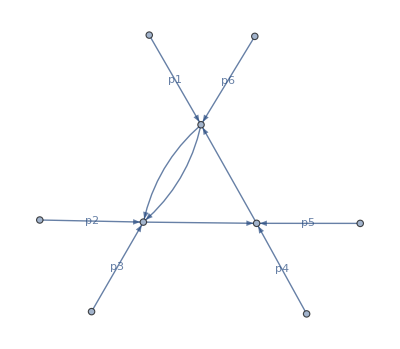

```mathematica
PureIntegralsNew[[123]]
plotDiagram[PureIntegralsNew[[123]]]
```

```mathematica
q[1]=p[2]+p[3]/.p4cons;
q[2]=p[4]+p[5];
q[3]=-q[1]-q[2];
intMasses={msq[1]->0,msq[2]->0,msq[3]->mt2};
modcayleyMat=Table[CayleyEntry[i,j],{i,0,3},{j,0,3}];
modcayleyMat//MatrixForm
kP=3+1;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]
convchange={v23->Expand[2 p[5]p[4]]/.mandelstamScalarProducts/.kinematics,q2->0,v45->s123};
BasisChange[3]=ep^3/LS*1/PR[2]
BasisChange[4]=ep^2((1-2ep)(q2+mt2+v23)/PR[8]-ep(q2+v23+v45)1/(2 PR[2]))/.convchange/.{s123->s23}
BasisChange[4]=ep^2 (-(ep (-s16+s23+s45))/(2 PR[2])+((1-2 ep) s45)/PR[8])
```

(0 | 1 | 1 | 1
1 | 0 | -s23 | mt2-s16
1 | -s23 | 0 | mt2-s45
1 | mt2-s16 | mt2-s45 | 2 mt2)

1/(2 root[s16^2-2 s16 s23+s23^2-2 s16 s45-2 s23 s45+s45^2])

(2 ep^3 root[s16^2-2 s16 s23+s23^2-2 s16 s45-2 s23 s45+s45^2])/PR[2]

ep^2 (-(ep (-mt2+s23+s45))/(2 PR[2])+((1-2 ep) s45)/PR[8])

ep^2 (-(ep (-s16+s23+s45))/(2 PR[2])+((1-2 ep) s45)/PR[8])

# Assemble basis

```mathematica
PureIntegralsOld[[{9,11,75,76,77,116,138,156,157}]][[-4;;]]
SelectInts={9,11,75,76,77,116,138,156,157};
SelectInts2=Join[SelectInts[[;;-5]],NewRepls];
NewRepls=Table[Position[PureIntegralsNew,PureIntegralsOld[[{9,11,75,76,77,116,138,156,157}]][[-4;;]][[i]]],{i,1,4}][[All,1,1]]
SubPureInts=PureIntegralsNew[[SelectInts2]];
SubPureInts[[8]]=Collect[SubPureInts[[9]]*BasisChange[1]//Expand,{_hxb,root[___]},Together]
SubPureInts[[9]]=Collect[SubPureInts[[9]]*BasisChange[2]//Expand,{_hxb,root[___]},Together]
SubPureInts[[6]]=Collect[SubPureInts[[7]]*BasisChange[3]//Expand,{_hxb,root[___]},Together]
SubPureInts[[7]]=Collect[SubPureInts[[7]]*BasisChange[4]//Expand,{_hxb,root[___]},Together]


Newsqrts=(Cases[SubPureInts,root[___],Infinity]//DeleteDuplicates)/.root[x_]:>x
Oldsqrts=(Cases[PureIntegralsNew,root[___],Infinity]//DeleteDuplicates)/.root[x_]:>x
sqrtSetNew=Join[Oldsqrts,Newsqrts]//DeleteDuplicates;
Export[FileNameJoin[{Directory[],"files/Roots.txt"}],sqrtSetNew];
Export[FileNameJoin[{NotebookDirectory[],"BubblePureInts.txt"}],SubPureInts];
```

{hxb[-1,1,0,1,0,1,0,1,0,0,0,0,0],hxb[0,1,0,1,0,1,0,1,0,0,0,0,0],hxb[1,0,0,1,0,1,0,1,-1,0,0,0,0],hxb[1,0,0,1,0,1,0,1,0,0,0,0,0]}

{123,141,158,159}

2 ep^3 hxb[2,0,0,1,0,1,0,1,0,0,0,0,0] root[mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2]

(ep^2 s45-2 ep^3 s45) hxb[1,0,0,1,0,1,0,2,0,0,0,0,0]+1/2 (ep^3 mt2-ep^3 s123-ep^3 s45) hxb[2,0,0,1,0,1,0,1,0,0,0,0,0]

2 ep^3 hxb[0,2,0,1,0,1,0,1,0,0,0,0,0] root[s16^2-2 s16 s23+s23^2-2 s16 s45-2 s23 s45+s45^2]

(ep^2 s45-2 ep^3 s45) hxb[0,1,0,1,0,1,0,2,0,0,0,0,0]+1/2 (ep^3 s16-ep^3 s23-ep^3 s45) hxb[0,2,0,1,0,1,0,1,0,0,0,0,0]

{s16^2-2 s16 s23+s23^2-2 s16 s45-2 s23 s45+s45^2,mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2}

{(-s12+s34)^2-2 (s12+s34) s56+s56^2,-4 s12 s23 s34 (-s123+s23-s234+s56)+(-s12 s23+s12 s234-s123 s234+s123 s34-s23 s34+s23 s56)^2,-4 mt2 s12+(-mt2-s12+s345)^2,-4 mt2 s56+s56^2,mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2,mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2,-4 mt2 s12 s34 s56+mt2^2 s56^2-2 mt2 s345 s56^2+s345^2 s56^2,mt2^2 s12^2-2 mt2^2 s12 s123+mt2^2 s123^2-2 mt2^2 s12 s34+2 mt2^2 s123 s34+2 mt2 s12 s123 s34-2 mt2 s123^2 s34+mt2^2 s34^2-2 mt2 s123 s34^2+s123^2 s34^2+2 mt2 s12 s123 s345-2 mt2 s123^2 s345-2 mt2 s123 s34 s345-2 s123^2 s34 s345+s123^2 s345^2-2 mt2 s12^2 s45+2 mt2 s12 s123 s45+4 mt2 s12 s34 s45-2 mt2 s123 s34 s45+2 s12 s123 s34 s45-2 mt2 s34^2 s45-2 s123 s34^2 s45-2 s12 s123 s345 s45+2 s123 s34 s345 s45+s12^2 s45^2-2 s12 s34 s45^2+s34^2 s45^2-2 mt2 s12 s345 s56+2 mt2 s123 s345 s56-2 mt2 s34 s345 s56+2 s123 s34 s345 s56-2 s123 s345^2 s56+2 mt2 s12 s45 s56-2 mt2 s123 s45 s56+2 mt2 s34 s45 s56-4 s12 s34 s45 s56+2 s123 s34 s45 s56+2 s12 s345 s45 s56+2 s123 s345 s45 s56+2 s34 s345 s45 s56-2 s12 s45^2 s56-2 s34 s45^2 s56+s345^2 s56^2-2 s345 s45 s56^2+s45^2 s56^2,s345^2-2 s345 s45+s45^2,mt2^2-2 mt2 s16+s16^2-2 mt2 s234-2 s16 s234+s234^2}

```mathematica
s={}
```